C:\Users\MrTLane\github\tight_binding_py

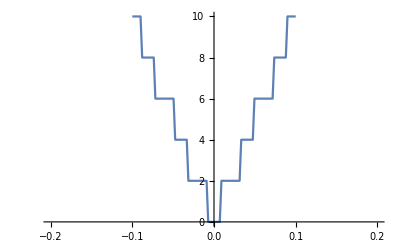

```mathematica
SetDirectory[NotebookDirectory[]]
fl=Import["test.csv","Table"];
data=Map[ToExpression@StringReplace[#,{"e"->"*^",","->""}]&,fl]/.j->I;
ListPlot[Re@data,Joined->True,PlotRange->{{-0.2, 0.2},{0,10}}]
```

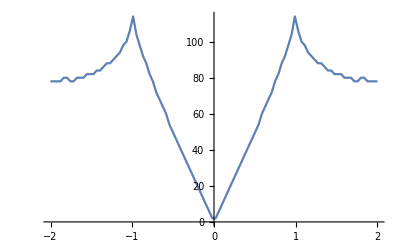

```mathematica
fl=Import["test_mlg.csv","Table"];
data=Map[ToExpression@StringReplace[#,{"e"->"*^",","->""}]&,fl]/.j->I;
ListPlot[Re@data,Joined->True,PlotRange->All]
```